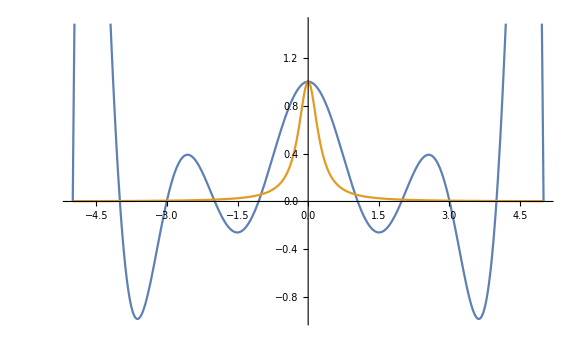

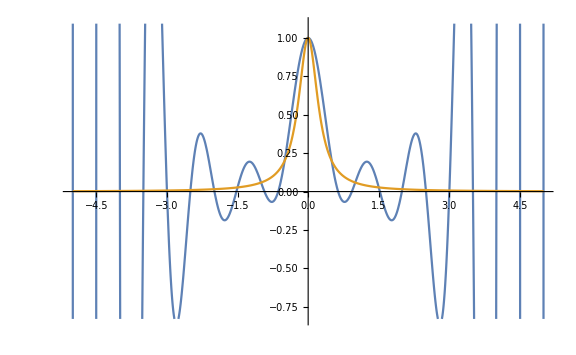

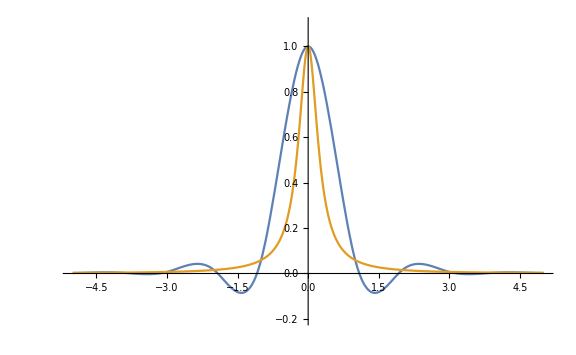

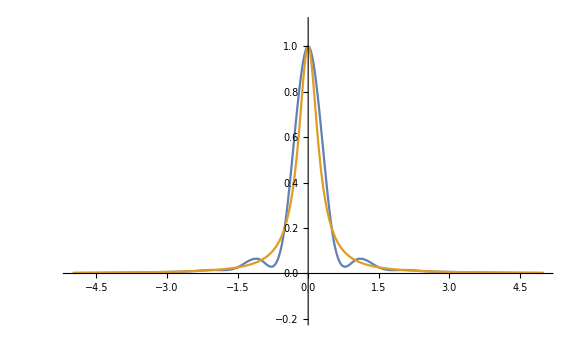

```mathematica
L10[x_]:=1.000000000000+-0.000000000000 x^1+-1.368979735575 x^2+-0.000000000000 x^3+0.489551943294 x^4+0.000000000000 x^5+-0.065181792600 x^6+0.000000000000 x^7+0.003496616985 x^8+0.000000000000 x^9+-0.000063502692 x^10

L20[x_]:=1.000000000000+0.000000000000 x^1+-4.816042806267 x^2+-0.000000000000 x^3+7.726541037896 x^4+-0.000000000000 x^5+-5.545023751005 x^6+-0.000000000000 x^7+2.091767295963 x^8+-0.000000000000 x^9+-0.452759391963 x^10+-0.000000000000 x^11+0.058749902266 x^12+0.000000000000 x^13+-0.004617545663 x^14+0.000000000000 x^15+0.000214093356 x^16+0.000000000000 x^17+-0.000005360830 x^18+-0.000000000000 x^19+0.000000055661 x^20

S10[x_]:=0.004185272241 (-4.000000000000-x)^3+-0.007968278172 (x--5.000000000000)^3+-0.001691506655 (-4.000000000000-x)+0.011859328755 (x--5.000000000000)/;-5.000000000000≤x≤-4.000000000000
S10[x_]:=-0.007968278172 (-3.000000000000-x)^3+0.029296056589 (x--4.000000000000)^3+0.011859328755 (-3.000000000000-x)+-0.022399504865 (x--4.000000000000)/;-4.000000000000≤x≤-3.000000000000
S10[x_]:=0.029296056589 (-2.000000000000-x)^3+-0.103733385664 (x--3.000000000000)^3+-0.022399504865 (-2.000000000000-x)+0.119118001049 (x--3.000000000000)/;-3.000000000000≤x≤-2.000000000000
S10[x_]:=-0.103733385664 (-1.000000000000-x)^3+0.420588336434 (x--2.000000000000)^3+0.119118001049 (-1.000000000000-x)+-0.361764807022 (x--2.000000000000)/;-2.000000000000≤x≤-1.000000000000
S10[x_]:=0.420588336434 (0.000000000000-x)^3+-0.680882403511 (x--1.000000000000)^3+-0.361764807022 (0.000000000000-x)+1.680882403511 (x--1.000000000000)/;-1.000000000000≤x≤0.000000000000
S10[x_]:=-0.680882403511 (1.000000000000-x)^3+0.420588336434 (x-0.000000000000)^3+1.680882403511 (1.000000000000-x)+-0.361764807022 (x-0.000000000000)/;0.000000000000≤x≤1.000000000000
S10[x_]:=0.420588336434 (2.000000000000-x)^3+-0.103733385664 (x-1.000000000000)^3+-0.361764807022 (2.000000000000-x)+0.119118001049 (x-1.000000000000)/;1.000000000000≤x≤2.000000000000
S10[x_]:=-0.103733385664 (3.000000000000-x)^3+0.029296056589 (x-2.000000000000)^3+0.119118001049 (3.000000000000-x)+-0.022399504865 (x-2.000000000000)/;2.000000000000≤x≤3.000000000000
S10[x_]:=0.029296056589 (4.000000000000-x)^3+-0.007968278172 (x-3.000000000000)^3+-0.022399504865 (4.000000000000-x)+0.011859328755 (x-3.000000000000)/;3.000000000000≤x≤4.000000000000
S10[x_]:=-0.007968278172 (5.000000000000-x)^3+0.004185272241 (x-4.000000000000)^3+0.011859328755 (5.000000000000-x)+-0.001691506655 (x-4.000000000000)/;4.000000000000≤x≤5.000000000000


S20[x_]:=0.000166149219 (-4.500000000000-x)^3+0.000352886737 (x--5.000000000000)^3+0.004945993867 (-4.500000000000-x)+0.006065624469 (x--5.000000000000)/;-5.000000000000≤x≤-4.500000000000
S20[x_]:=0.000352886737 (-4.000000000000-x)^3+0.000270063958 (x--4.500000000000)^3+0.006065624469 (-4.000000000000-x)+0.007714585178 (x--4.500000000000)/;-4.500000000000≤x≤-4.000000000000
S20[x_]:=0.000270063958 (-3.500000000000-x)^3+0.001534569765 (x--4.000000000000)^3+0.007714585178 (-3.500000000000-x)+0.009768641823 (x--4.000000000000)/;-4.000000000000≤x≤-3.500000000000
S20[x_]:=0.001534569765 (-3.000000000000-x)^3+-0.001325798666 (x--3.500000000000)^3+0.009768641823 (-3.000000000000-x)+0.014124553115 (x--3.500000000000)/;-3.500000000000≤x≤-3.000000000000
S20[x_]:=-0.001325798666 (-2.500000000000-x)^3+0.013240855162 (x--3.000000000000)^3+0.014124553115 (-2.500000000000-x)+0.016491766408 (x--3.000000000000)/;-3.000000000000≤x≤-2.500000000000
S20[x_]:=0.013240855162 (-2.000000000000-x)^3+-0.031804126694 (x--2.500000000000)^3+0.016491766408 (-2.000000000000-x)+0.038720262443 (x--2.500000000000)/;-2.500000000000≤x≤-2.000000000000
S20[x_]:=-0.031804126694 (-1.500000000000-x)^3+0.163245942471 (x--2.000000000000)^3+0.038720262443 (-1.500000000000-x)+0.013242568436 (x--2.000000000000)/;-2.000000000000≤x≤-1.500000000000
S20[x_]:=0.163245942471 (-1.000000000000-x)^3+-0.459946917249 (x--1.500000000000)^3+0.013242568436 (-1.000000000000-x)+0.232633788136 (x--1.500000000000)/;-1.500000000000≤x≤-1.000000000000
S20[x_]:=-0.459946917249 (-0.500000000000-x)^3+2.551581472155 (x--1.000000000000)^3+0.232633788136 (-0.500000000000-x)+-0.237895368039 (x--1.000000000000)/;-1.000000000000≤x≤-0.500000000000
S20[x_]:=2.551581472155 (0.000000000000-x)^3+-4.475790736078 (x--0.500000000000)^3+-0.237895368039 (0.000000000000-x)+3.118947684019 (x--0.500000000000)/;-0.500000000000≤x≤0.000000000000
S20[x_]:=-4.475790736078 (0.500000000000-x)^3+2.551581472155 (x-0.000000000000)^3+3.118947684019 (0.500000000000-x)+-0.237895368039 (x-0.000000000000)/;0.000000000000≤x≤0.500000000000
S20[x_]:=2.551581472155 (1.000000000000-x)^3+-0.459946917249 (x-0.500000000000)^3+-0.237895368039 (1.000000000000-x)+0.232633788136 (x-0.500000000000)/;0.500000000000≤x≤1.000000000000
S20[x_]:=-0.459946917249 (1.500000000000-x)^3+0.163245942471 (x-1.000000000000)^3+0.232633788136 (1.500000000000-x)+0.013242568436 (x-1.000000000000)/;1.000000000000≤x≤1.500000000000
S20[x_]:=0.163245942471 (2.000000000000-x)^3+-0.031804126694 (x-1.500000000000)^3+0.013242568436 (2.000000000000-x)+0.038720262443 (x-1.500000000000)/;1.500000000000≤x≤2.000000000000
S20[x_]:=-0.031804126694 (2.500000000000-x)^3+0.013240855162 (x-2.000000000000)^3+0.038720262443 (2.500000000000-x)+0.016491766408 (x-2.000000000000)/;2.000000000000≤x≤2.500000000000
S20[x_]:=0.013240855162 (3.000000000000-x)^3+-0.001325798666 (x-2.500000000000)^3+0.016491766408 (3.000000000000-x)+0.014124553115 (x-2.500000000000)/;2.500000000000≤x≤3.000000000000
S20[x_]:=-0.001325798666 (3.500000000000-x)^3+0.001534569765 (x-3.000000000000)^3+0.014124553115 (3.500000000000-x)+0.009768641823 (x-3.000000000000)/;3.000000000000≤x≤3.500000000000
S20[x_]:=0.001534569765 (4.000000000000-x)^3+0.000270063958 (x-3.500000000000)^3+0.009768641823 (4.000000000000-x)+0.007714585178 (x-3.500000000000)/;3.500000000000≤x≤4.000000000000
S20[x_]:=0.000270063958 (4.500000000000-x)^3+0.000352886737 (x-4.000000000000)^3+0.007714585178 (4.500000000000-x)+0.006065624469 (x-4.000000000000)/;4.000000000000≤x≤4.500000000000
S20[x_]:=0.000352886737 (5.000000000000-x)^3+0.000166149219 (x-4.500000000000)^3+0.006065624469 (5.000000000000-x)+0.004945993867 (x-4.500000000000)/;4.500000000000≤x≤5.000000000000
k[x_] := 1 / (1 + 16 * x^2)

Plot[{L10[x],k[x]},{x,-5,5}, ImageSize->Large]
Plot[{L20[x],k[x]},{x,-5,5}, ImageSize->Large]
Plot[{S10[x],k[x]},{x,-5,5}, ImageSize->Large, PlotRange->{-0.2,1.1}]
Plot[{S20[x],k[x]},{x,-5,5}, ImageSize->Large, PlotRange->{-0.2,1.1}]
```